```mathematica
gpdu=Import["G:\\calc-online\\gpd\\3dre\\gpd3d-f-up-xi1-baryon-polarize.wdx"];
Hdgu1=Query[1,1]@gpdu;
Hdgu2=Query[1,2]@gpdu;
Heru=Query[1,3]@gpdu;
Hdau=Query[1,4]@gpdu;
Edgu1=Query[2,1]@gpdu;
Edgu2=Query[2,2]@gpdu;
Eeru=Query[2,3]@gpdu;
Edau=Query[2,4]@gpdu;
Hdgfu1=Interpolation[Flatten[Hdgu1,1]];
Hdgfu2=Interpolation[Flatten[Hdgu2,1]];
Herfu=Interpolation[Flatten[Heru,1]];
Hdafu=Interpolation[Flatten[Hdau,1]];
Edgfu1=Interpolation[Flatten[Edgu1,1]];
Edgfu2=Interpolation[Flatten[Edgu2,1]];
Eerfu=Interpolation[Flatten[Eeru,1]];
Edafu=Interpolation[Flatten[Edau,1]];
```

```mathematica
Herall2[x_,t_]:=Herfu[x,-t]+Hdafu[x,-t];
Eerall2[x_,t_]:=Eerfu[x,-t]+Edafu[x,-t];
```

```mathematica
pHd2=Show[Plot3D[I*Hdgfu1[x,-t],{x,0.8,1},{t,0.1,1},PlotRange->All],Plot3D[I*Hdgfu2[x,-t],{x,0.1,0.8},{t,0.1,1},PlotRange->All],Plot3D[I*Herall2[x,t],{x,-0.1,0.1},{t,0.1,1},PlotRange->All],
Graphics3D[Text[Style["x",Black,35,FontSlant->Italic,FontFamily->Times],Scaled[{0.42,-0.22,0.1}]]],Graphics3D[Text[Rotate[Style["-t (GeV^2)",Black,30,FontFamily->Times],280Degree],Scaled[{-0.18,-0.1,0.65}]]],Graphics3D[Text[Style["H_d",Black,30,FontFamily->Times],Scaled[{1.16,0,0.6}]]],AxesStyle->Directive[{Black,Thickness[0.003]},12],AxesEdge->{{-1,-1},{-1,-1},{1,-1}},BoxStyle->Directive[{Black,Thickness[0.003]}],TicksStyle->Directive[20,FontFamily->Times],ImageSize->600,ViewPoint->{-0.7,-2,0.8}]
pEd2=Show[Plot3D[Re[I*Edgfu1[x,-t]],{x,0.8,1},{t,0.1,1},PlotRange->All],Plot3D[Re[I*Edgfu2[x,-t]],{x,0.1,0.8},{t,0.1,1},PlotRange->All],Plot3D[Re[I*Eerall2[x,t]],{x,-0.1,0.1},{t,0.1,1},PlotRange->All],
Graphics3D[Text[Style["x",Black,35,FontSlant->Italic,FontFamily->Times],Scaled[{0.42,-0.22,0.1}]]],Graphics3D[Text[Rotate[Style["-t (GeV^2)",Black,30,FontFamily->Times],280Degree],Scaled[{-0.18,-0.1,0.65}]]],Graphics3D[Text[Style["E_d",Black,30,FontFamily->Times],Scaled[{1.18,0,0.6}]]],AxesStyle->Directive[{Black,Thickness[0.003]},12],AxesEdge->{{-1,-1},{-1,-1},{1,-1}},BoxStyle->Directive[{Black,Thickness[0.003]}],TicksStyle->Directive[20,FontFamily->Times],ImageSize->600,ViewPoint->{-0.7,-2,0.8}]
```

-Graphics3D-

-Graphics3D-

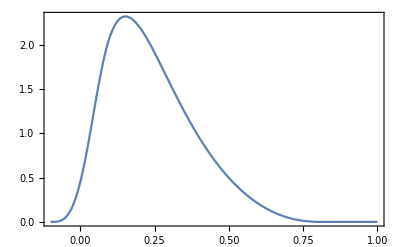
-Graphics-H_dx

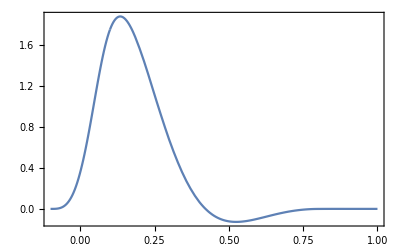
-Graphics-E_dx

```mathematica
pHd2d2=Labeled[Show[Plot[I*Hdgfu1[x,-1],{x,0.8,1},PlotRange->All],Plot[I*Hdgfu2[x,-1],{x,0.1,0.8},PlotRange->All],Plot[I*Herall2[x,1],{x,-0.1,0.1},PlotRange->All],Frame->True,FrameStyle->Directive[Thick,20]],
{"H_d",
"x"},{Left,Bottom},LabelStyle->24]
pEd2d2=Labeled[Show[Plot[I*Edgfu1[x,-1],{x,0.8,1},PlotRange->All],Plot[I*Edgfu2[x,-1],{x,0.1,0.8},PlotRange->All],Plot[Re[I*Eerall2[x,1]],{x,-0.1,0.1},PlotRange->All],Frame->True,FrameStyle->Directive[Thick,20]],
{"E_d",
"x"},{Left,Bottom},LabelStyle->24]
```

```mathematica
pathH2d2=FileNameJoin[{"C:\\Users\\DELL\\Desktop\\73diagram",
"H2d-f-polar.pdf"}];
Export[pathH2d2,pHd2d2]
pathE2d2=FileNameJoin[{"C:\\Users\\DELL\\Desktop\\73diagram",
"E2d-f-polar.pdf"}];
Export[pathE2d2,pEd2d2]
```

C:\Users\DELL\Desktop\73diagram\H2d-f-polar.pdf

C:\Users\DELL\Desktop\73diagram\E2d-f-polar.pdf